Computational Physics

# Title. Dynamical Systems and Chaos

Paul Abbott

School of Physics, M013
University of Western Australia
35 Stirling Highway
Crawley WA 6009, Australia
paul@physics.uwa.edu.au
physics.uwa.edu.au/~paul

Title.Section Planar Pendulum

The equation of motion of a simple pendulum is

θ̈(t)+ω^2 sin(θ(t))=0, ω^2=g/l,

where m is the mass of the bob, l is the length of the pedulum, and θ is the angle measured from the vertical direction with clockwise positive.

Usually, only the harmonic approximation (i.e., sin(θ) is replaced by θ) of the simple pendulum equation is considered:

θ̈(t)+ω^2 θ(t)=0.

Here, the more general equation (which includes damping when β ≠ 0 and a sinusoidal driving term when α ≠ 0)

θ̈(t)+β θ̇(t)+ω^2 sin(θ(t))=α sin(ω_d t)

will be examined. The units of mass, length, and time are chosen so that they are all equal to unity, i.e., we are working with dimensionless variables.

### Title.Section.Subsection Undamped pendulum

The dimensionless equation for the undamped pendulum in Mathematica notation reads

```mathematica
𝒫=θ''(t)+sin(θ(t))==0;
```

Exercise. Use NDSolve to numerically solve 𝒫 for θ for 10 units of time ("seconds") with the initial conditions, θ(0)==0 and θ'(0)==1 and call the result 𝓊. (NB. It is more convenient to solve for θ rather than θ(t)). Display a phase-space plot by pairing up the angle and angular velocity values using {θ(t),θ'(t)}/.First[𝓊] and visualize the motion using ParametricPlot. Describe the trajectory that results. [3]

```mathematica
𝓊=First@NDSolve[{𝒫,θ(0)==0,θ'(0)==1},θ,{t,0,10}]
```

{θ→InterpolatingFunction[(0. | 10.),<>]}

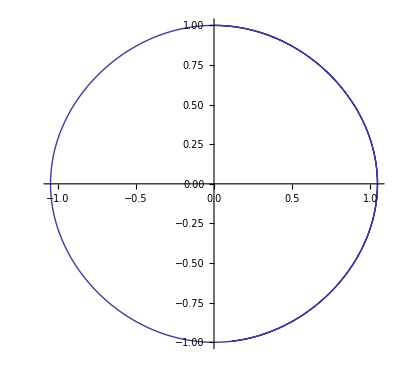

```mathematica
ParametricPlot[Evaluate[{θ(t),θ'(t)}/.𝓊],{t,0,10}]
```

Almost a circle in phase-space.

Note that we are using the first (in this case there is only one) numerical solution to the differential equation and computing its derivative (θ'(t)) numerically.

Exercise. Increase the initial velocity, θ'(0), to something slightly less than 2 and redo Exercise. Explain what is happening here. [2]

```mathematica
𝓊=First@NDSolve[{𝒫,θ(0)==0,θ'(0)==1.95},θ,{t,0,15}]
```

{θ→InterpolatingFunction[(0. | 15.),<>]}

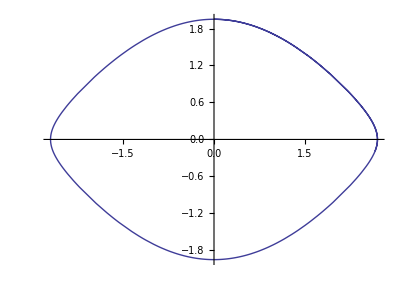

```mathematica
ParametricPlot[Evaluate[{θ(t),θ'(t)}/.𝓊],{t,0,15}]
```

Phase-space plot is now flattened. Maximum angle is almost π.

Exercise. Set θ'(0) to 2 and redo Exercise, but over a longer time interval. Explain what is happening here. [2]

```mathematica
𝓊=First@NDSolve[{𝒫,θ(0)==0,θ'(0)==2},θ,{t,0,200}]
```

{θ→InterpolatingFunction[(0. | 200.),<>]}

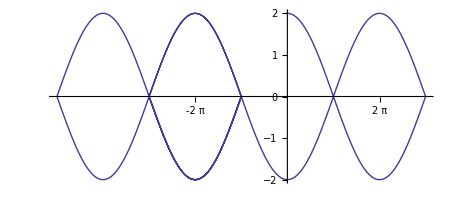

```mathematica
ParametricPlot[Evaluate[{θ(t),θ'(t)}/.𝓊],{t,0,200},PlotRange->All,Ticks->{π Range[-10,10],Automatic}]
```

With θ'(0)==2, we have the critical (angular) velocity for which the pendulum reaches the top (θ=π) with zero velocity.

Exercise. Explain the critical value of θ'(0) from an energy viewpoint (Hint: the kinetic energy is proportional to 1/2 (θ'(t))^2 and the initial potential energy is 0. What is the total energy at the top of the loop?). [3]

Potential energy is V=m g h; At bottom  V=0 and at top is V=2m g l. Kinetic energy is T=1/2 I ω^2=1/2 m l^2(θ'(t))^2. Total energy is E=T+V=m g h+1/2 m l^2(θ'(t))^2=1/2 m g l ((2h)/l+l/g(θ'(t))^2). Energy at bottom equals that at top ⟹(θ'(0))^2=2 since ω^2=g/l=1.

### Title.Section.Subsection Damped pendulum

The equation for the damped pendulum (where the damping is proportional to the velocity) can be written

```mathematica
𝒫=θ''(t)+β θ'(t)+sin(θ(t))==0;
```

Exercise. Solve the equation numerically for the damped pendulum with damping  β→0.2 and initial conditions θ(0)==0 and θ'(0)==1 for 20 seconds. Display a phase-space plot and interpret the result. [3]

```mathematica
𝓊=First@NDSolve[{𝒫/.β->0.2,θ(0)==0,θ'(0)==1},θ,{t,0,20}]
```

{θ→InterpolatingFunction[(0. | 20.),<>]}

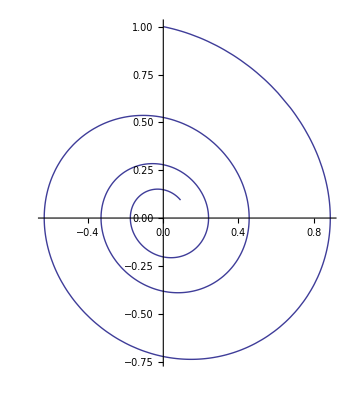

```mathematica
ParametricPlot[Evaluate[{θ(t),θ'(t)}/.𝓊],{t,0,20},PlotRange->All]
```

### Title.Section.Subsection Damped driven pendulum

The equation for the damped driven pendulum can be written

```mathematica
𝒫=θ''(t)+β θ'(t)+sin(θ(t))==α cos(ω t);
```

Exercise. Solve the equation numerically for the damped driven pendulum with {β→0.2,α→0.52,ω→0.694} and initial conditions {θ(0)==0.8,θ'(0)==0.8} for 400 seconds and call the result 𝒹. You will need to increase the number of time-steps by playing with the MaxSteps option of NDSolve. Display a phase-space plot of {θ(t),θ'(t)} using ParametricPlot with AspectRatio → 1/4 and interpret the result. [3]

Exercise. Physically, since the angle θ∈[-π,π], it makes more sense to examine (θ-π) mod (2 π). Display a phase-space plot of {(θ(t)-π) mod (2 π),θ'(t)} and interpret the result. [3]

You should see that the resulting phase-space diagram is periodic (in the language of chaos it shows a period-3 limit cycle).

The Poincaré section provides a simplification of the phase diagram by sampling at time intervals equal to the period of the driving frequency.

Exercise. Compute the period using τ=(2 π)/ω. How many cycles were present in the first 100 seconds? [2]

To avoid transient effects, the data for the first few cycles should be discarded.

Exercise. Visualize the Poincaré section by applying ListPlot to a table of values of {(θ(t)-π) mod (2 π),θ'(t)} between t=10τ (i.e., discarding the first 10 cycles) and 400 in steps of τ. Interpret the result. [3]

### Title.Section.Subsection Series solution

The easiest way to get Mathematica to solve differential equations such as y''(x)+k^2 y(x)=0 using series methods is direct expansion of the equation, i.e.,

```mathematica
eqn=y''(x)+k^2 y(x)+(O(x))^7==0
```

(y(0) k^2+y''(0))+(y'(0) k^2+y^(3)(0)) x+1/2 (y''(0) k^2+y^(4)(0)) x^2+1/6 (y^(3)(0) k^2+y^(5)(0)) x^3+1/24 (y^(4)(0) k^2+y^(6)(0)) x^4+1/120 (y^(5)(0) k^2+y^(7)(0)) x^5+1/720 (y^(6)(0) k^2+y^(8)(0)) x^6+O(x^7)==0

This is equivalent to expanding y(x) (and y''(x)) into a power series.

```mathematica
yseries=y(x)+(O(x))^7
```

y(0)+y'(0) x+1/2 y''(0) x^2+1/6 y^(3)(0) x^3+1/24 y^(4)(0) x^4+1/120 y^(5)(0) x^5+1/720 y^(6)(0) x^6+O(x^7)

You can see that the expression multiplying each power of x in the expansion of y''(x)+k^2 y(x) must vanish identically, i.e., y(0) k^2+y''(0)=0, y'(0) k^2+y^(3)(0)=0, …   To see the equations generated you can use LogicalExpand (this step is not required).

```mathematica
LogicalExpand[eqn]
```

y(0) k^2+y''(0)==0∧y'(0) k^2+y^(3)(0)==0∧1/2 (y''(0) k^2+y^(4)(0))==0∧1/6 (y^(3)(0) k^2+y^(5)(0))==0∧1/24 (y^(4)(0) k^2+y^(6)(0))==0∧1/120 (y^(5)(0) k^2+y^(7)(0))==0∧1/720 (y^(6)(0) k^2+y^(8)(0))==0

Note that the initial conditions, y(0) and y'(0) are not determined but that you can solve for the undetermined coefficients (y''(0), y^(3)(0), …) in terms of the initial conditions.

```mathematica
Solve[eqn,Table[Derivative[n][y](0),{n,2,8}]]
```

{{y^(7)(0)→-k^6 y'(0),y^(8)(0)→k^8 y(0),y^(5)(0)→k^4 y'(0),y^(3)(0)→-k^2 y'(0),y^(6)(0)→-k^6 y(0),y^(4)(0)→k^4 y(0),y''(0)→-k^2 y(0)}}

To obtain the series solution to the original equation you substitute these coefficients into the series expansion of y(x).

```mathematica
yseries/.First[%]
```

y(0)+y'(0) x-1/2 (k^2 y(0)) x^2-1/6 (k^2 y'(0)) x^3+1/24 k^4 y(0) x^4+1/120 k^4 y'(0) x^5-1/720 (k^6 y(0)) x^6+O(x^7)

If you now supply the initial conditions — say y(0)=1 and y'(0)=0 — you get

```mathematica
%/.{y(0)->1,y'(0)->0}
```

1-(k^2 x^2)/2+(k^4 x^4)/24-(k^6 x^6)/720+O(x^7)

### Title.Section.Subsection Series solution for the undamped pendulum

We would like to analytically solve the equation

θ''(t)+ω^2 sin(θ(t))=0.

Exercise. Obtain the series solution to equation (Title.Section.Equation) up to tenth order using the method of §Title.Section.Subsection for the initial conditions, {θ(0)→α,θ'(0)→0}. (Hint: it is a good idea to find the series solution to lower order first to check that you are doing the right thing.) [5]

```mathematica
Solve[θ''(t)+ω^2 sin(θ(t))+O[t]^8==0,Table[Derivative[n][θ](0),{n,2,9}]]/.{θ(0)->α,θ'(0)->0}
```

{{θ^(8)(0)→1/2 ω^2 (17 ω^6 cos(3 α)-15 ω^6 cos(α)) sin(α),θ^(9)(0)→0,θ^(7)(0)→0,θ^(6)(0)→1/2 (4 ω^6 sin(α)-2 ω^6 sin(3 α)),θ^(5)(0)→0,θ^(4)(0)→ω^4 cos(α) sin(α),θ^(3)(0)→0,θ''(0)→-ω^2 sin(α)}}

```mathematica
seriessolution=Factor[TrigReduce[#]]&/@(θ(t)+O[t]^9/.{θ(0)->α,θ'(0)->0}/.Last[%])
```

α-1/2 (ω^2 sin(α)) t^2+1/48 ω^4 sin(2 α) t^4+1/720 ω^6 (2 sin(α)-sin(3 α)) t^6-((ω^8 (32 sin(2 α)-17 sin(4 α))) t^8)/161280+O(t^9)

The linearized equation results by replacing sin(θ) by θ.

θ''(t)+ω^2 θ(t)=0.

Exercise. Solve the linearized equation (Title.Section.Equation) taking into account the initial conditions. To what order do these solutions agree? (Hint: you can take the difference between the series solution and the exact solution to the linearized equation and simplify.) What does the difference say about the behaviour over a long period of time? [6]

## Title.Section Iterative Operations

This section presents four examples of visualizing iterative operations.

### Title.Section.Subsection Julia set

The (quadratic) Julia set associated to a fixed complex number c is found by iterating the map z↦z^2+c. The set of points, z, that do not escape to infinity (i.e., their absolute value remains bounded, say |z|<2, after m iterations have been carried out) is the Julia set.

Exercise. Enter the function f[z_]:=z^2+0.5ⅈ, i.e., starting at c = 0.5 ⅈ. Using NestList, iterate f ten times, starting at z = 0.1. Compute the absolute value of these complex numbers. Are they remaining bounded? Try z = 0.5 and z = 1 and comment. [5]

The following Mathematica procedural code (i.e., similar in style to Fortran, C, Pascal, Basic,…) iterates z=z^2+c for a particular value of c.  Either the value of z escapes to ∞ which can be tested using |z|<2.0 or it hops around a finite number of times, bounded above by m.

```mathematica
JuliaModule[w_,c_,m_]:=Module[{z=w,n=0},While[|z|<2∧n<m,z=z^2+c;++n];n];
```

Alternatively, we can implement this as a pure function (using Function) with {w,c,m} as dummy arguments.

```mathematica
JuliaFunction=Function[{w,c,m},Module[{z=w,n=0},While[|z|<2∧n<m,z=z^2+c;++n];n]];
```

A table of values using either implementation is somewhat slow:

```mathematica
Table[JuliaModule[x+ⅈ y,1+0.3 ⅈ,35],{x,-1.5,1.5,0.1},{y,-1.5,1.5,0.1}];//Timing//First
```

0.041254

```mathematica
Table[JuliaFunction[x+ⅈ y,1+0.3 ⅈ,35],{x,-1.5,1.5,0.1},{y,-1.5,1.5,0.1}];//Timing//First
```

0.045302

Numerical function compilation, using Compile, is a useful way of speeding up a computation. The following code expects three arguments: the point z, the point c, and the maximum number of iterations.

```mathematica
JuliaCompile=Compile[({{w, _Complex}, {c, _Complex}, {m, _Integer}}),Module[{z=w,n=0},While[|z|<2∧n<m,z=z^2+c;n++];n]];
```

Exercise. Compare the speed of JuliaCompile and JuliaFunction. [1 Mark]

```mathematica
Table[JuliaCompile[x+ⅈ y,1+0.3 ⅈ,35],{x,-1.5,1.5,0.1},{y,-1.5,1.5,0.1}];//Timing//First
```

0.009691

I don't expect you to get into the details of Compile — just know that it can make code faster. For numerical functions, it is often advantageous writing them using Function because it is straightforward to "compile" a function: usually it is only a matter of replacing Function with Compile and "typing" the arguments.

Compile assumes its arguments should be compiled as machine-precision real numbers unless it is directed to do otherwise by variable declarations such as {w,_Complex} and {m,_Integer}.

The first argument of Compile is a list of lists (i.e., a rank-2 tensor or matrix) and is typeset in TraditionalForm as a matrix. You can either enter it as an n×2 matrix:

```mathematica
({{w, _Complex}, {c, _Complex}, {m, _Integer}})
```

or as a list of lists:

```mathematica
{{w,_Complex},{c,_Complex},{m,_Integer}}
```

The variable types appearing in the Module part of JuliaCompile are guessed based on the first time they are set. Since the local variable z is first initialized to w, Compile knows it is a complex variable. Similarly, the statement n=0 indicates to Compile that n is an integer.

Exercise. Use DensityPlot to visualize the Julia set over [-1.5, 1.5] × [-1.3, 1.3] in the complex plane for c = ⅈ. [2]

Algorithms for computing fractal sets often involve iterating a formula until a specified condition is met. By default, FixedPoint and FixedPointList stop iterating when two successive calculations give the same result. To specify our own stopping condition, we can use the SameTest option. This option takes a pure function of two arguments that returns True if the two arguments can be considered “the same”. For example, here we iterate the square root function, applied to 10, and stop when two successive values are within 0.1 of each other.

```mathematica
FixedPoint[Sqrt,10.0,SameTest->(|#1-#2|<0.1&)]
```

1.07461

Exercise. Find a FixedPoint of cos(x), stopping when two successive values are within 10^-5 of each other. [2]

```mathematica
FixedPoint[Cos,1.,SameTest->(|#1-#2|<10^-5&)]
```

0.739082

Here is an alternative implementation of JuliaCompile using a fixed number of iterations (here 35).

```mathematica
JuliaCompile=Compile[({{z, _Complex}, {c, _Complex}}),Length[FixedPointList[#1^2+c&,z,35,SameTest->(|#2|>2.0&)]]];
```

```mathematica
Table[JuliaCompile[x+ⅈ y,1+0.3 ⅈ],{x,-1.5,1.5,0.1},{y,-1.5,1.5,0.1}];//Timing//First
```

0.036042

Using SameTest→(|#2|>2.0&) tests whether the last value (i.e., #2) generated by FixedPointList remains bounded (i.e., |z|<2). The length of the result of FixedPointList is the number of iterations.

Exercise. Plot the Julia set associated with c=0.27334+0.00742 ⅈ over z∈[-1.2, 1.2] × [-1.2, 1.2]. [2]

```mathematica
DensityPlot[-JuliaCompile[x+ⅈ y,0.27334+0.00742 ⅈ],{x,-1.2,1.2},{y,-1.2,1.2},Frame->False,Axes->False,PlotPoints->100]
```

-Graphics-

Exercise. Interact with the plot of exercise Exercise to find a point that is in the Julia set, i.e., click on the graphic, hold down the Apple key (i.e., ⌘) on a Macintosh or the Control key (i.e., Ctrl) under Windows, and move the mouse around.  The mouse-coordinates will appear in the status box (bottom left corner of the Notebook).  Click at an appropriate point and copy the coordinate value(s) using Copy (⌘-C or Ctrl-V). Paste this value into the Notebook (in a new cell) and check that it is in the Julia set by applying JuliaComplie to it. (Note that Complex @@ {a, b} yields the complex number Complex[a, b]). [2]

For fun, run the following code to produce an array of plots with z∈[-1.1-1.1ⅈ,1.1+1.1ⅈ] and c=a+b ⅈ∈[-2-ⅈ,1+ⅈ].

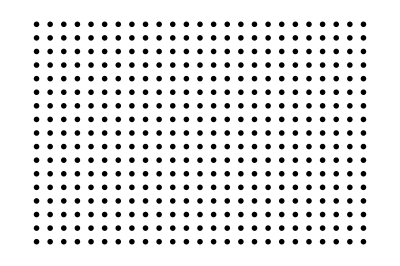

```mathematica
GraphicsGrid[Table[DensityPlot[-JuliaCompile[x+ⅈ y,a+b ⅈ],{x,-1.1,1.1},{y,-1.1,1.1},Frame->False,Axes->False,PlotPoints->10],{b,-1,1,1/8},{a,-2,1,1/8}]]
```

### Title.Section.Subsection The Mandelbrot set

The (standard) Mandelbrot set is the set of points, c, obtained from the quadratic recurrence equation, z_n=z_(n-1)^2+c, with z_0=c, for which the orbit of z_n remains finite. In other words, pick a point c=x+ⅈ y and compute c, c^2+c, (c^2+c)^2+c, …

```mathematica
NestList[z↦z^2+c,c,3]
```

{c,c^2+c,(c^2+c)^2+c,((c^2+c)^2+c)^2+c}

If the iterates remain bounded then c is in the set.

```mathematica
Manipulate[Module[{c=Complex@@z},Length@FixedPointList[z↦z^2+c,c,35,SameTest->({a,b}↦Abs[b]>2.0)]],{z,{-2,-1.5},{0.8,1.5}}]
```

It turns out that points in the Mandelbrot set have connected Julia sets.

Exercise. Modify the Julia code to compute and visualize the Mandelbrot set. [6]

```mathematica
MandelbrotCompile=Compile[{{c,_Complex}},Length[FixedPointList[z↦z^2+c,c,35,SameTest->({a,b}↦Abs[b]>2.0)]]];
```

```mathematica
DensityPlot[-MandelbrotCompile[x+ⅈ y],{x,-2,0.8},{y,-1.5,1.5},Frame->False,Axes->False,PlotPoints->100,ColorFunction->"DarkRainbow",AspectRatio->Automatic]
```

-Graphics-

### Title.Section.Subsection Newton's Method

Consider using Newton's method to compute the (complex) argument of the n-th roots of unity, i.e., the roots of f(z)=z^n-1. The Newton iteration, z→z-(f(z))/(f'(z)), becomes

```mathematica
z-(f(z))/(f'(z))/.f->Function[z,z^n-1]//Simplify
```

(z (z^-n+n-1))/n

To evaluate both f(z) and f'(z) we use a pure function replacement rule for f, f→Function(z,z^n-1).

The compiled function

```mathematica
NewtonIteration=Compile[({{n, _Integer}, {c, _Complex}}),Arg[FixedPoint[Function[z,(z (z^-n+n-1))/n],c,35]]];
```

can be used to show the convergence of points in the complex plane for specific n.

Exercise. For n=4, visualize to which “attracting” root (out of ±1 and ±ⅈ) the Newton iteration converges. Note that the color of each point is determined by the Arg of the attracting root Arg({+1,-1,+ⅈ,-ⅈ}). Interpret the result. [4]

For fun, run the following code to produce an array of graphics (generated using GraphicsArray) that show the convergence of points in the complex plane, for n ranging from 5 to 13.

```mathematica
GraphicsGrid[Partition[Table[DensityPlot[NewtonIteration[n,x+ⅈ y],{x,1.1,-1.1},{y,-1.1,1.1},PlotPoints->50,Frame->False],{n,5,13}],3],Spacings->Scaled[0.05]]
```

-Graphics-

### Title.Section.Subsection Feigenbaum Bifurcation Diagram

The Feigenbaum bifurcation diagram shows the behavior of iterates of x↦λ x (1-x) and displays the period-doubling route to chaos. The following code iterates this mapping 300 times using NestList and then deletes the first 100 iterations (during which time the iteration “settles down”).

```mathematica
DSolve[x-(f(x))/(f'(x))==x (1-x) λ,f,x]
```

{{f→({x}↦c_1 ⅇ^((log((x-1) λ+1)-log(x))/(λ-1)))}}

c_1 (((x-1) λ+1)/x)^(1/(λ-1))

```mathematica
ContourPlot[(((x-1) λ+1)/x)==0,{λ,1,4},{x,0.01,1},PlotPoints->50]
```

-Graphics-

```mathematica
Plot[{2-1/x,√(3-2/x),((4 (x-1)+1)/x)^(1/3)},{x,0,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[(((x-1) λ+1)/x)^(1/(λ-1)),{x,0,1},PlotRange->({{0, 1}, {0, 1}})],{λ,1+10^-6,4}]
```

```mathematica
Manipulate[Plot[Evaluate[MapIndexed[{x,n}↦Tooltip[x,First[n]-1],NestList[x↦x (1-x) λ,x,5]]],{x,0,1},PlotRange->{0,1},AspectRatio->Automatic],{λ,1,4}]
```

```mathematica
NestList[x↦3.0x (1-x),0.1,10]
```

{0.1,0.27,0.5913,0.724993,0.598135,0.721109,0.603333,0.717967,0.607471,0.71535,0.610873}

```mathematica
Plot[Nest[x↦3.679`30x (1-x),x,20],{x,0,1},PlotPoints->200,PlotRange->{0,1},WorkingPrecision->30,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Reduce[(((x-1) λ+1)/x)^(1/(λ-1))==0,x]//Simplify
```

Re(λ)>1∧x+1/λ==1

```mathematica
Plot3D[(((x-1) λ+1)/x)^(1/(λ-1)),{x,0,1},{λ,1,4},PlotRange->All,Mesh->False]
```

-Graphics3D-

```mathematica
Feigenbaum=Compile[({{λ, _Real}}),({λ,#}&)/@Drop[NestList[x↦λ x (1-x),0.2,300],100]];
```

Exercise. λvalues=Flatten[Table[Feigenbaum[λ],{λ,1.0,4.0,0.005}],1]; generates a table of iterated values for λ ranging from 1 to 4 in steps of 0.005.  Visualize Union[λvalues] using ListPlot. (Union eliminates duplicates.) Where does period-doubling commence? [3]

```mathematica
λvalues=Flatten[Table[Feigenbaum[λ],{λ,1.0,4.0,0.005}],1];
```

```mathematica
ListPlot[Union[λvalues]]
```

-Graphics-

Exercise. Use Fvalues=Last/@λvalues; to obtain a list of Feigenbaum[λ] values. Listen to Fvalues using ListPlay. Describe what you hear. [3]